#### Bayesian Networks and Influence Diagrams

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
(*ber[p_,x_]=p^x(1-p)^(1-x);
pri=ber[θ1,fuel]ber[θ2,spark];
left=ber[θ3,gauge](1-fuel)+ber[θ4,gauge]fuel;
right=ber[θ5,start](1-fuel)(1-spark)+ber[θ6,start](1-fuel)spark+ber[θ7,start]fuel(1-spark)+ber[θ8,start]fuel spark;
U[fuel_,spark_,gauge_,start_]=PowerExpand[-Log[pri left right]]//Simplify
QS = Import["./car.csv","CSV"];
Sum[Apply[U,QS[[i,;;]]],{i,1,Length[QS]}]//Simplify*)
```

```mathematica
(*energy=-364 Log[1-θ1]-999636 Log[θ1]-50140 Log[1-θ2]-949860 Log[θ2]-360 Log[1-θ3]-4 Log[θ3]-948 Log[1-θ4]-998688 Log[θ4]-Log[1-θ5]-356 Log[1-θ6]-7 Log[θ6]-4903 Log[1-θ7]-45236 Log[θ7]-9412 Log[1-θ8]-940085 Log[θ8]/.Map[(#->1/(1+Exp[-#]))&,{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8}]*)
```

```mathematica
energy=-1280 Log[1-θ1]-998720 Log[θ1]-49744 Log[1-θ2]-950256 Log[θ2]-1272 Log[1-θ3]-8 Log[θ3]-1000 Log[1-θ4]-997720 Log[θ4]-62 Log[1-θ5]-2 Log[θ5]-1207 Log[1-θ6]-9 Log[θ6]-4914 Log[1-θ7]-44766 Log[θ7]-9373 Log[1-θ8]-939667 Log[θ8];
U[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_]=energy(*+Total[Map[(PowerExpand[-Log[Simplify[PDF[BetaDistribution[.5,.5],x],0<x<1]]]/.x->#)&,{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8}]]*);
dU[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_]=Simplify[GradientG[U[θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8],{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8}]];
ddU[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_]=Diagonal[Simplify[HessianH[U[θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8],{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8}]]];
```

```mathematica
Dim=8;
KU=1;
STEPS=5;
CHAINS=5;
INTERVAL=1001;
diag=True;
outbnd[q_]:=AnyTrue[q,(#>=1||#<=0)&];
qinit=RandomVariate[UniformDistribution[{0,1}],{CHAINS,Dim}];
QS=hmc[U,dU,ddU,Dim,5000,10000,True,True,qinit];
```

10011.44472×10^615.3730.4057040.542641.4431×10^62.88782×10^62.88782×10^61.1×10^-70.00766191True0.1

20021.42126×10^60.00114410.2255190.4364591.42126×10^62.84252×10^62.84251×10^64.24098×10^-80.00125278False0.1

30031.42113×10^623.95170.4338070.5179091.42113×10^62.84226×10^62.84226×10^64.24098×10^-80.00103536True0.1

40041.42113×10^60.0006331390.4469560.5138761.42112×10^62.84225×10^62.84225×10^64.24098×10^-80.00137806False0.1

50051.42113×10^625.58230.2932720.4152591.42113×10^62.84227×10^62.84226×10^64.66507×10^-80.00113889True0.1

60061.42112×10^60.00342820.2977230.2973191.42114×10^62.84227×10^62.84226×10^64.66507×10^-80.00113889False0.1

70071.42114×10^619.92720.5081140.4886581.42113×10^62.84227×10^62.84226×10^64.66507×10^-80.00113889True0.1

80081.42113×10^60.00006665120.2185320.4384951.42113×10^62.84227×10^62.84226×10^64.66507×10^-80.00113889False0.1

90091.42113×10^615.97730.3168630.41661.42113×10^62.84227×10^62.84226×10^64.66507×10^-80.00113889True0.1

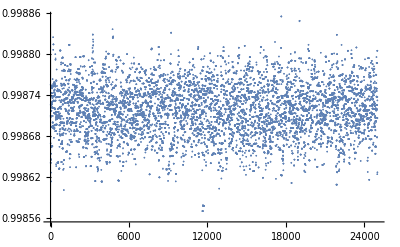
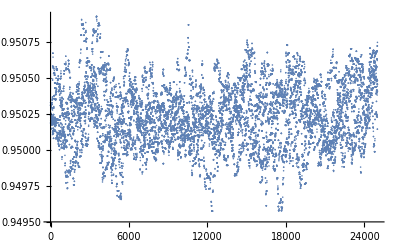
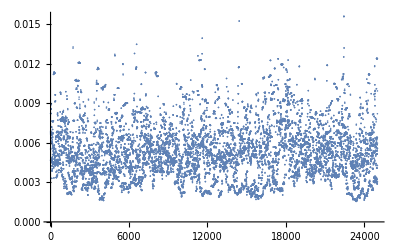
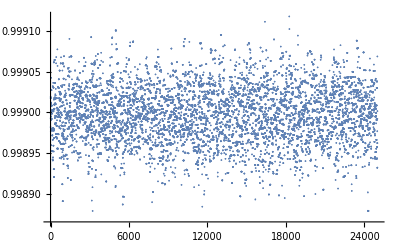
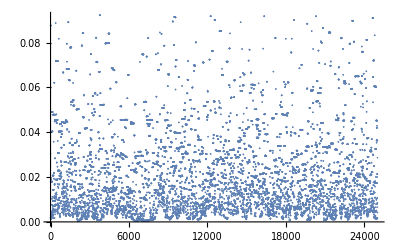
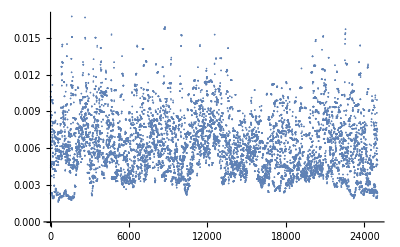
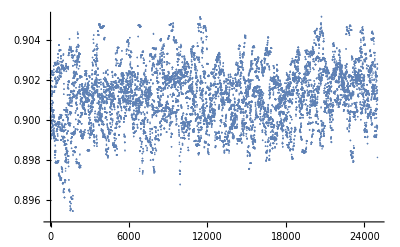
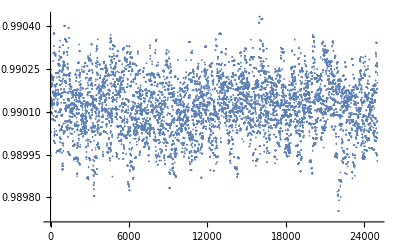

```mathematica
Table[ListPlot[QS[[;;,i]]],{i,1,8}]
```

```mathematica
Mean[QS]
```

{0.998719,0.950241,0.00536271,0.998998,0.0231059,0.00628877,0.901185,0.990121}

```mathematica
StandardDeviation[QS]
```

{0.0000361229,0.000213199,0.00202624,0.0000320703,0.0201672,0.00238096,0.00145321,0.0000989248}